```mathematica
Task 1
```

```mathematica
(*Var 1*)
```

```mathematica
a = 1^2+121*1;
```

```mathematica
x[n_]:=a^n/(n!)
```

```mathematica
h1 = Plot[x[n], {n, 120, 122}]
```

-Graphics-

```mathematica
D[x[n], n]
```

(122^n Log[122])/(n!)-(122^n Gamma[1+n] PolyGamma[0,1+n])/(n!)^2

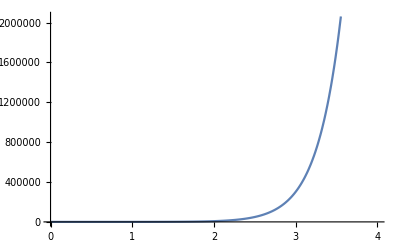

```mathematica
h2 = Plot[x[n], {n, 0, 4}]
```

```mathematica
FindMaximum[x[n],{n, 120, 122}]
```

{3.48181×10^51,{n→121.5}}

```mathematica
(*функция монотонно возрастает для всех значений 0≤n≤121.5; после этого функция монотонно убывает и стремится к 0 (придел посчитан ниже) *)
```

Set::write: Tag Times in 3 h is Protected.

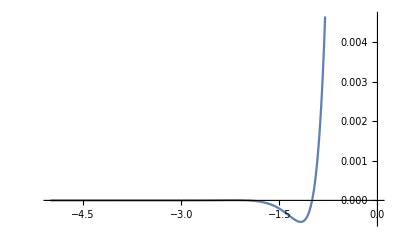

```mathematica
3h = Plot[x[n], {n, -5,0}]
```

```mathematica
NMinimize[x[n], {-2≤n≤-1}]
```

NMinimize::ivar: -2≤n≤-1 is not a valid variable.

NMinimize[122^n/(n!),{-2≤n≤-1}]

```mathematica
(*при отрицательных значениях функция ведет себя неоднозначно (по идее, факториал определен только на неотрицательных значениях параметра, но вольфрам что-то рисует). можно заметить монотонное возрастание начиная с некого элемента *)
```

```mathematica
T1 = Table[x[n], {n, 0, 10}]
```

{1,122,7442,907924/3,27691682/3,3378385204/15,206081497444/45,25141942688168/315,383414625994562/315,46776584371336564/2835,2853371646651530404/14175}

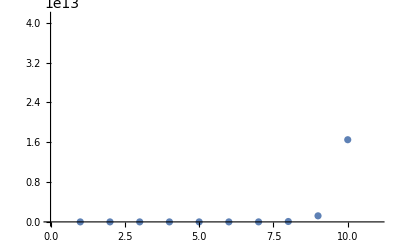

```mathematica
h2 = ListPlot[T1]
```

```mathematica
Limit[x[n], n->∞]
```

0

```mathematica
ListPlot[{{ 121.5,3.481*10^51}},PlotStyle->{PointSize[0.026],Red}]
```

-Graphics-

```mathematica
x[121.5]
```

3.48181×10^51

```mathematica
plot1 = Show[h1,  ListPlot[{{ 121.5,3.4818115909525166*^51}},PlotStyle->{PointSize[0.026],Red}], PlotLegends->{function, "Local Maximum"},GridLines->{{},{3.4818115909525166*^51}}]
```

-Graphics-

```mathematica
ShowLegend[plot1,{{{Graphics[{Blue,Line[{{0,0},{2,0}}]}],"function"},{Graphics[{Red,Line[{{0,0},{2,0}}]}],"local maximum"}},
LegendPosition->{0.7,-0.3},LegendSize->{0.45,0.4},LegendShadow->False}]
```

-Graphics-

```mathematica
a[n_]:= Piecewise[{{n^2+121n, 1≤n<10}, {n^2,10≤n≤20}, {n^2-10n,20<n≤30}}]
```

```mathematica
Clear[x]
```

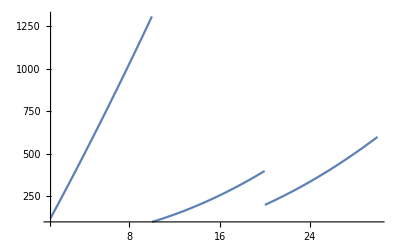

```mathematica
Plot[a[x], {x,1,30} ]
```

```mathematica
T11 = Table[a[n],{n,1,30}]
```

{122,246,372,500,630,762,896,1032,1170,100,121,144,169,196,225,256,289,324,361,400,231,264,299,336,375,416,459,504,551,600}

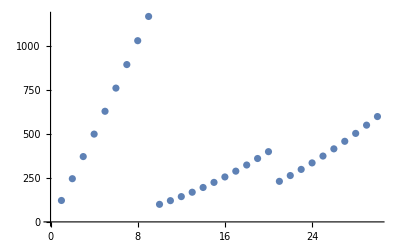

```mathematica
ListPlot[T11]
```

```mathematica
Task 2
Clear[f, h, h1, h2, x, g ]
```

2 Task

```mathematica
f[x_]:=(x^4+16)/x
```

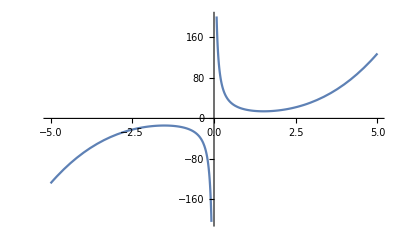

```mathematica
h2 = Plot[f[x], {x,-5,5}, PlotLegends->"function"]
```

```mathematica
(*x < 0 : f[x] < 0
x > 0 : f[x] > 0*)
```

```mathematica
Reduce[D[f[x],x]==0, Reals]
```

x==-2/3^(1/4)||x==2/3^(1/4)

```mathematica
(*for x ≤ -2/3^(1/4) : increases monotonically; 
for -2/3^(1/4)≤x<=2/3^(1/4) \ {0} : decreases monotonically; x==0 - breaking point; for x>=2/3^(1/4) : increases monotonically *)
```

```mathematica
Reduce[D[D[f[x],x],x]>0, Reals]
```

x>0

```mathematica
Reduce[D[D[f[x],x],x]<0, Reals]
```

x<0

```mathematica
(*for x < 0 : f[x] - the graph of the function is convex;
for x < 0: f[x] - function graph is concave;
x==0 - inflection current*)
```

```mathematica
l11 = Limit[f[x]/x, x->∞]
```

∞

```mathematica
l21 = Limit[f[x]/x,x->∞]
```

∞

```mathematica
(*oblique and horizontal asymptotes do not exist
there is one vertical asymptote : x==0*)
```

```mathematica
(*The linearized function is equal to the linear part of the Taylor series
Let's look ot x==3*)
```

```mathematica
Normal[Series[f[x],{x,3,1}]]
```

97/3+227/9 (-3+x)

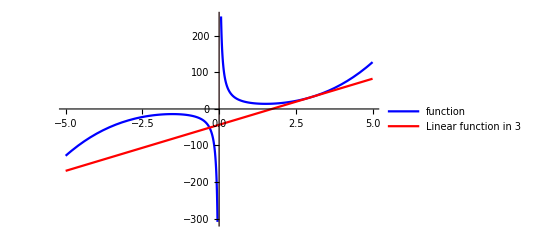

```mathematica
h3 = Plot[{f[x],%}, {x,-5,5},GridLines->{{{0,Red}},None}, PlotStyle->{Blue, Red}, PlotLegends->{"function","Linear function in 3"}]
```

```mathematica
T2 = Table[f[x], {x, 1, 10}]
```

{17,16,97/3,68,641/5,656/3,2417/7,514,6577/9,5008/5}

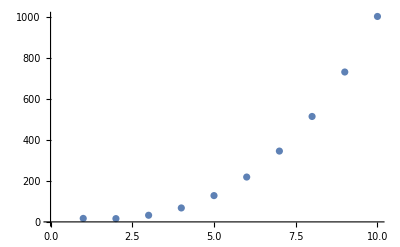

```mathematica
h4 = ListPlot[T2]
```

```mathematica
l1=Graphics@Line[{{-5, f[-2/3^(1/4)]},{5,f[-2/3^(1/4)]}}];
l2=Graphics@Line[{{-5, f[2/3^(1/4)]},{5,f[2/3^(1/4)]}}];
```

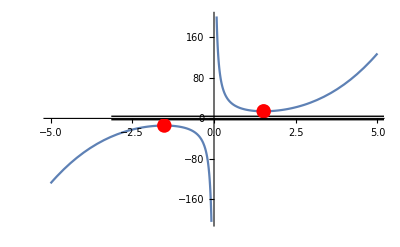

```mathematica
plot2 = Show[h2,l1,l2,  ListPlot[{{ -2/3^(1/4),f[-2/3^(1/4)]}, {2/3^(1/4),f[2/3^(1/4)]}},PlotStyle->{PointSize[0.026],Red}]]
```

```mathematica
Task 3
```

```mathematica
Clear[f, h, h1, h2, x, g ]
```

```mathematica
f[x_]:=Cos[x]+x/2
```

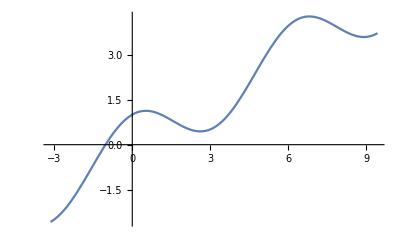

```mathematica
h1 = Plot[f[x], {x, -π, 3π}]
```

```mathematica
Reduce[D[f[x],x]==0 && x≥-π && x ≤ 3π, x]
```

x==π/6||x==(5 π)/6||x==(13 π)/6||x==(17 π)/6

```mathematica
(*локальные экстремумы написаны выше. вот их значеня:*)
```

```mathematica
f[π/6]//N
```

1.12782

```mathematica
f[(5π)/6]//N
```

0.442972

```mathematica
f[(13 π)/6]//N
```

4.26942

```mathematica
f[(17 π)/6]//N
```

3.58456

```mathematica
(*очевидно, что минимальное значение - левая граница, а максимальная - 2й справа экстремум*)
```

```mathematica
min = f[-π]
```

-1-π/2

```mathematica
max = f[(13 π)/6]
```

(√3)/2+(13 π)/12

```mathematica
l1=Graphics@Line[{{-π, max},{3π,max}}];
```

```mathematica
l2 = Graphics@Line[{{-π, min},{3π,min}}];
```

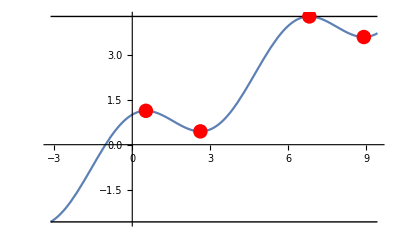

```mathematica
Show[h1, l1,l2,ListPlot[{{π/6 ,f[π/6]}, {(5 π)/6,f[(5 π)/6]}, {(13 π)/6, f[(13 π)/6]}, {(17 π)/6, f[(17 π)/6]}},PlotStyle->{PointSize[0.026],Red}] ]
```

```mathematica
T3 = Table[f[x], {x, 1, 10}]
```

{1/2+Cos[1],1+Cos[2],3/2+Cos[3],2+Cos[4],5/2+Cos[5],3+Cos[6],7/2+Cos[7],4+Cos[8],9/2+Cos[9],5+Cos[10]}

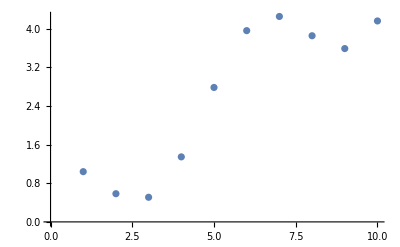

```mathematica
ListPlot[T3]
```

```mathematica
Task 4
```

```mathematica
Clear[f, x, y, d, hd, h1,h2]
```

```mathematica
f[x_,y_]:=x^2+2x*y-4x+8y
```

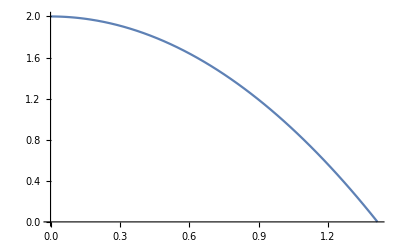

```mathematica
hd = Plot[{2-x^2},{x,0,Sqrt[2]}] (*Область определения*)
```

```mathematica
r1 = ImplicitRegion[x≥0,{x,y}]
```

ImplicitRegion[x≥0,{x,y}]

```mathematica
r2 = ImplicitRegion[y≥0,{x,y}]
```

ImplicitRegion[y≥0,{x,y}]

```mathematica
r3=ImplicitRegion[y≤2-x^2,{x,y}]
```

ImplicitRegion[y≤2-x^2,{x,y}]

```mathematica
d=RegionIntersection[r1,r2,r3]
```

ImplicitRegion[x≥0&&y≥0&&x^2+y≤2,{x,y}]

```mathematica
Plot3D[f[x,y], {x,y}∈d, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*Наименьшее значение, судя по графику, при x==Sqrt[2], y==0;
Наибольшее значение,  судя по графику, при x==0, y==2 *)
```

```mathematica
maxzn=f[0,2]
```

16

```mathematica
minzn = f[Sqrt[2],0]
```

2-4 √2